```mathematica
ClearAll["Global`*"]
```

```mathematica
n = 40
y = {-2.57251482,0.33806206,2.71757796,1.09861336,2.85603752,-0.91651351,0.15555127,-2.68160347,2.47043789,3.47459025,1.63949862,-1.32148757,2.64187513,0.30357848,-4.09546231,-1.50709863,-0.99517866,-2.0648892,-2.40317949,3.46383544,0.91173696,1.18222221,0.04235722,-0.52815171,1.15551598,-1.62749724,0.71473237,-1.08458812,4.66020296,1.24563831,-0.67970862,0.93461681,1.18187607,-1.49501051,2.44755622,-2.06424237,-0.04584074,1.93396696,1.07685273,-0.09837907}
```

40

{-2.57251,0.338062,2.71758,1.09861,2.85604,-0.916514,0.155551,-2.6816,2.47044,3.47459,1.6395,-1.32149,2.64188,0.303578,-4.09546,-1.5071,-0.995179,-2.06489,-2.40318,3.46384,0.911737,1.18222,0.0423572,-0.528152,1.15552,-1.6275,0.714732,-1.08459,4.6602,1.24564,-0.679709,0.934617,1.18188,-1.49501,2.44756,-2.06424,-0.0458407,1.93397,1.07685,-0.0983791}

```mathematica
epslist = Range[ -3,3,0.03]
```

{-3.,-2.97,-2.94,-2.91,-2.88,-2.85,-2.82,-2.79,-2.76,-2.73,-2.7,-2.67,-2.64,-2.61,-2.58,-2.55,-2.52,-2.49,-2.46,-2.43,-2.4,-2.37,-2.34,-2.31,-2.28,-2.25,-2.22,-2.19,-2.16,-2.13,-2.1,-2.07,-2.04,-2.01,-1.98,-1.95,-1.92,-1.89,-1.86,-1.83,-1.8,-1.77,-1.74,-1.71,-1.68,-1.65,-1.62,-1.59,-1.56,-1.53,-1.5,-1.47,-1.44,-1.41,-1.38,-1.35,-1.32,-1.29,-1.26,-1.23,-1.2,-1.17,-1.14,-1.11,-1.08,-1.05,-1.02,-0.99,-0.96,-0.93,-0.9,-0.87,-0.84,-0.81,-0.78,-0.75,-0.72,-0.69,-0.66,-0.63,-0.6,-0.57,-0.54,-0.51,-0.48,-0.45,-0.42,-0.39,-0.36,-0.33,-0.3,-0.27,-0.24,-0.21,-0.18,-0.15,-0.12,-0.09,-0.06,-0.03,0.,0.03,0.06,0.09,0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36,0.39,0.42,0.45,0.48,0.51,0.54,0.57,0.6,0.63,0.66,0.69,0.72,0.75,0.78,0.81,0.84,0.87,0.9,0.93,0.96,0.99,1.02,1.05,1.08,1.11,1.14,1.17,1.2,1.23,1.26,1.29,1.32,1.35,1.38,1.41,1.44,1.47,1.5,1.53,1.56,1.59,1.62,1.65,1.68,1.71,1.74,1.77,1.8,1.83,1.86,1.89,1.92,1.95,1.98,2.01,2.04,2.07,2.1,2.13,2.16,2.19,2.22,2.25,2.28,2.31,2.34,2.37,2.4,2.43,2.46,2.49,2.52,2.55,2.58,2.61,2.64,2.67,2.7,2.73,2.76,2.79,2.82,2.85,2.88,2.91,2.94,2.97,3.}

```mathematica
pmu1[mu1_]:=PDF[NormalDistribution[0,5], mu1]*Boole[-2<= mu1 && mu1 <= 2]
```

```mathematica
pmu2[mu2_]:=PDF[NormalDistribution[0,5], mu2]*Boole[-2<= mu2 && mu2 <= 2]
```

```mathematica
pmu3[mu3_, eps1_, eps2_]:=PDF[NormalDistribution[0+eps1,5+eps2], mu3]*Boole[-2<= mu3 && mu3 <= 2]
```

```mathematica
pu[mu1_, mu2_, mu3_, eps1_, eps2_]:=pmu1[mu1] * pmu2[mu2] * pmu3[mu3,eps1, eps2]
```

```mathematica
L[mu1_, mu2_, mu3_, y_]:= PDF[NormalDistribution[3.0*mu1*mu2-mu3,1],y]
```

```mathematica
For[i=1, i<=n,i++, 
pu[mu1_, mu2_, mu3_, eps1_, eps2_]=pu[mu1, mu2, mu3,eps1, eps2] * L[mu1, mu2, mu3, y[[i]]];
]
```

```mathematica
norm = NIntegrate[pu[mu1,mu2,mu3, eps1=0,eps2=0],{mu1,-2,2},{mu2,-2,2}, {mu3,-2,2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.53745×10^-52 and 1.63239×10^-57 for the integral and error estimates.

1.53745×10^-52

```mathematica
p[mu1_,mu2_,mu3_]:= pu[mu1, mu2, mu3, eps1=0, eps2=0]/ norm
```

```mathematica
ArgMax[p[mu1,mu2,mu3],{mu1,mu2,mu3}]
```

{-0.000106377,-0.000106274,-0.311331}

```mathematica
mu3Range = Range[-2,2,0.02];
```

```mathematica
{t, mu3Table}= Timing[ Table[NIntegrate[p[mu1,mu2,mu3], {mu1, -∞, ∞}, {mu2, -∞, ∞}], {mu3, mu3Range}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{216.542,{0.270859,0.273011,0.275187,0.277386,0.27961,0.281858,0.284132,0.286432,0.288758,0.291112,0.293494,0.295905,0.298346,0.300817,0.30332,0.305854,0.308423,0.311025,0.313663,0.316337,0.319048,0.321798,0.324589,0.32742,0.330295,0.333213,0.336178,0.33919,0.342251,0.345364,0.34853,0.35175,0.355029,0.358367,0.361768,0.365234,0.368768,0.372373,0.376053,0.379811,0.383651,0.387577,0.391595,0.395708,0.399923,0.404245,0.408681,0.413238,0.417925,0.42275,0.427723,0.432856,0.438161,0.443654,0.449351,0.455271,0.461437,0.467874,0.474612,0.481682,0.489123,0.496976,0.505286,0.514099,0.523466,0.533432,0.544041,0.555328,0.567315,0.580003,0.59337,0.607364,0.621895,0.636833,0.652006,0.667198,0.682154,0.696585,0.710179,0.722612,0.733563,0.742733,0.749857,0.754725,0.757187,0.757172,0.754683,0.749804,0.742688,0.733556,0.722675,0.710349,0.696898,0.682645,0.667899,0.652947,0.638036,0.623379,0.609141,0.595447,0.582382,0.569994,0.558303,0.547303,0.536972,0.527273,0.518164,0.509596,0.501521,0.493893,0.486667,0.479803,0.473263,0.467017,0.461035,0.455292,0.449767,0.444441,0.439298,0.434322,0.429502,0.424826,0.420285,0.415869,0.411572,0.407385,0.403303,0.399319,0.395428,0.391625,0.387906,0.384266,0.380703,0.377211,0.373789,0.370432,0.367138,0.363904,0.360729,0.357608,0.354541,0.351525,0.348558,0.345639,0.342765,0.339936,0.337148,0.334402,0.331696,0.329027,0.326396,0.323801,0.321241,0.318714,0.31622,0.313757,0.311326,0.308924,0.306551,0.304207,0.30189,0.2996,0.297335,0.295096,0.292882,0.290692,0.288525,0.286382,0.28426,0.282161,0.280082,0.278025,0.275987,0.27397,0.271972,0.269993,0.268033,0.266091,0.264167,0.26226,0.260371,0.258498,0.256641,0.254801,0.252977,0.251168,0.249375,0.247596,0.245832,0.244083,0.242347,0.240626,0.238918,0.237224,0.235544,0.233876,0.232221,0.230578,0.228949,0.227331,0.225725}}

```mathematica
mu3norm = Total[mu3Table]
mu3Table = mu3Table/mu3norm
mu3TrueCDF= Table[Function[upto,Sum[mu3Table[[i]], {i, 1,upto}]][i], {i,1, Length[mu3Table]}]
```

82.3947

{0.00328733,0.00331346,0.00333986,0.00336656,0.00339354,0.00342083,0.00344843,0.00347634,0.00350457,0.00353314,0.00356205,0.00359131,0.00362094,0.00365093,0.0036813,0.00371207,0.00374323,0.00377482,0.00380683,0.00383928,0.00387219,0.00390557,0.00393944,0.0039738,0.00400869,0.00404411,0.00408009,0.00411665,0.0041538,0.00419158,0.00423,0.00426909,0.00430888,0.0043494,0.00439067,0.00443273,0.00447562,0.00451938,0.00456404,0.00460965,0.00465626,0.00470391,0.00475267,0.00480259,0.00485374,0.0049062,0.00496004,0.00501535,0.00507223,0.00513079,0.00519115,0.00525344,0.00531783,0.0053845,0.00545364,0.00552549,0.00560033,0.00567845,0.00576022,0.00584604,0.00593635,0.00603166,0.0061325,0.00623947,0.00635315,0.0064741,0.00660287,0.00673986,0.00688533,0.00703932,0.00720156,0.0073714,0.00754775,0.00772905,0.0079132,0.00809758,0.0082791,0.00845425,0.00861924,0.00877013,0.00890304,0.00901433,0.0091008,0.00915987,0.00918976,0.00918957,0.00915937,0.00910014,0.00901379,0.00890295,0.0087709,0.00862129,0.00845804,0.00828506,0.0081061,0.00792462,0.00774366,0.00756577,0.00739296,0.00722677,0.0070682,0.00691785,0.00677596,0.00664246,0.00651707,0.00639936,0.0062888,0.00618481,0.00608682,0.00599423,0.00590653,0.00582322,0.00574386,0.00566805,0.00559544,0.00552575,0.00545869,0.00539405,0.00533163,0.00527123,0.00521274,0.00515599,0.00510087,0.00504729,0.00499513,0.00494431,0.00489477,0.00484641,0.00479919,0.00475304,0.0047079,0.00466373,0.00462048,0.0045781,0.00453656,0.00449582,0.00445584,0.0044166,0.00437806,0.00434018,0.00430296,0.00426636,0.00423035,0.00419492,0.00416004,0.0041257,0.00409187,0.00405854,0.00402569,0.00399331,0.00396138,0.00392988,0.0038988,0.00386814,0.00383787,0.00380798,0.00377847,0.00374932,0.00372052,0.00369207,0.00366395,0.00363615,0.00360867,0.0035815,0.00355463,0.00352804,0.00350175,0.00347573,0.00344998,0.0034245,0.00339927,0.0033743,0.00334958,0.00332509,0.00330085,0.00327683,0.00325304,0.00322947,0.00320611,0.00318297,0.00316004,0.00313731,0.00311478,0.00309245,0.00307031,0.00304835,0.00302659,0.003005,0.00298359,0.00296236,0.0029413,0.00292041,0.00289968,0.00287912,0.00285872,0.00283848,0.0028184,0.00279846,0.00277868,0.00275905,0.00273956}

{0.00328733,0.00660079,0.00994065,0.0133072,0.0167008,0.0201216,0.02357,0.0270463,0.0305509,0.0340841,0.0376461,0.0412374,0.0448584,0.0485093,0.0521906,0.0559027,0.0596459,0.0634207,0.0672275,0.0710668,0.074939,0.0788446,0.082784,0.0867578,0.0907665,0.0948106,0.0988907,0.103007,0.107161,0.111353,0.115583,0.119852,0.124161,0.12851,0.132901,0.137334,0.141809,0.146329,0.150893,0.155502,0.160158,0.164862,0.169615,0.174418,0.179271,0.184178,0.189138,0.194153,0.199225,0.204356,0.209547,0.214801,0.220118,0.225503,0.230957,0.236482,0.242082,0.247761,0.253521,0.259367,0.265303,0.271335,0.277468,0.283707,0.29006,0.296534,0.303137,0.309877,0.316762,0.323802,0.331003,0.338375,0.345922,0.353651,0.361565,0.369662,0.377941,0.386396,0.395015,0.403785,0.412688,0.421702,0.430803,0.439963,0.449153,0.458342,0.467502,0.476602,0.485616,0.494519,0.503289,0.511911,0.520369,0.528654,0.53676,0.544685,0.552428,0.559994,0.567387,0.574614,0.581682,0.5886,0.595376,0.602018,0.608535,0.614935,0.621223,0.627408,0.633495,0.639489,0.645396,0.651219,0.656963,0.662631,0.668226,0.673752,0.679211,0.684605,0.689937,0.695208,0.700421,0.705577,0.710677,0.715725,0.72072,0.725664,0.730559,0.735405,0.740204,0.744958,0.749665,0.754329,0.75895,0.763528,0.768064,0.77256,0.777016,0.781433,0.785811,0.790151,0.794454,0.79872,0.80295,0.807145,0.811305,0.815431,0.819523,0.823582,0.827607,0.831601,0.835562,0.839492,0.843391,0.847259,0.851097,0.854905,0.858683,0.862432,0.866153,0.869845,0.873509,0.877145,0.880754,0.884335,0.88789,0.891418,0.89492,0.898395,0.901845,0.90527,0.908669,0.912043,0.915393,0.918718,0.922019,0.925296,0.928549,0.931778,0.934984,0.938167,0.941327,0.944465,0.947579,0.950672,0.953742,0.956791,0.959817,0.962822,0.965806,0.968768,0.971709,0.97463,0.97753,0.980409,0.983267,0.986106,0.988924,0.991723,0.994501,0.99726,1.}

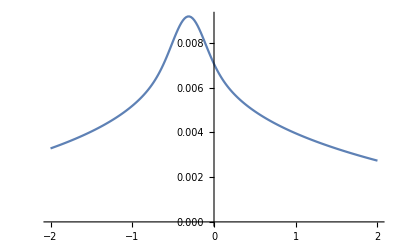

```mathematica
ListLinePlot[Transpose[{mu3Range,mu3Table}],PlotRange->{Automatic,Full}]
```

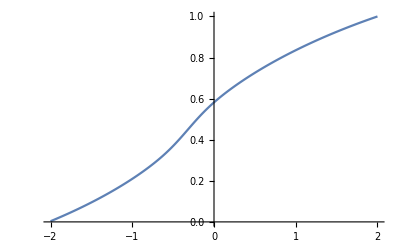

```mathematica
ListLinePlot[Transpose[{mu3Range,mu3TrueCDF}],PlotRange->{Automatic,Full}]
```

```mathematica
matrix = Table[0,{r,Length[mu3Range]},{c, Length[epslist]}]
```

{1}
 |  |  |  |

```mathematica
For[i = 1, i <= Length[epslist], i++,
 eps = epslist[[i]];
 norm = NIntegrate[pu[mu1, mu2, mu3, eps1 = 0, eps2 = eps], {mu1, -2, 2}, {mu2, -2, 2}, {mu3, -2, 2}];
 p[mu1_, mu2_, mu3_] := pu[mu1, mu2, mu3, eps1=0, eps2=eps]/ norm;
mu3Table=  Table[NIntegrate[p[mu1,mu2,mu3], {mu1, -∞, ∞}, {mu2, -∞, ∞}], {mu3, mu3Range}];
mu3norm = Total[mu3Table];
mu3Table = mu3Table/mu3norm;
mu3CDF= Table[Function[upto,Sum[mu3Table[[i]], {i, 1,upto}]][i], {i,1, Length[mu3Table]}];
matrix[[All,i]] = mu3CDF;
 ]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.71368×10^-52 and 2.57607×10^-57 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.66309×10^-52 and 2.55115×10^-57 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.61381×10^-52 and 2.52463×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
MatrixForm[matrix]
```

(1)
 |  |  |  |

```mathematica
KS = Table[Max[Abs[matrix[[All, i]] - mu3TrueCDF]],{i,1,Length[epslist]}]
```

{0.0252716,0.0244284,0.0236192,0.0228429,0.0220969,0.0213798,0.0206901,0.0200266,0.0193878,0.0187726,0.01818,0.0176088,0.017058,0.0165267,0.016014,0.0155191,0.0150412,0.0145794,0.0141331,0.0137017,0.0132845,0.0128808,0.0124901,0.0121119,0.0117456,0.0113908,0.011047,0.0107137,0.0103905,0.010077,0.00977293,0.00947778,0.00919127,0.00891305,0.00864283,0.00838028,0.00812514,0.00787712,0.00763597,0.00740152,0.00717345,0.00695152,0.00673552,0.00652524,0.00632049,0.00612106,0.00592679,0.00573749,0.005553,0.00537316,0.00519781,0.00502681,0.00486001,0.00469729,0.0045385,0.00438353,0.00423225,0.00408455,0.00394031,0.00379944,0.00366182,0.00352736,0.00339596,0.00326753,0.00314199,0.00301924,0.0028992,0.0027818,0.00266696,0.00255461,0.00244467,0.00233708,0.00223177,0.00212868,0.00202774,0.0019289,0.0018321,0.00173728,0.0016444,0.00155338,0.0014642,0.0013768,0.00129113,0.00120714,0.00112481,0.00104407,0.000964888,0.000887229,0.000811052,0.00073632,0.000662996,0.000591044,0.000520432,0.000451127,0.000383096,0.000316308,0.000250733,0.000186343,0.000123109,0.0000610035,2.22045×10^-16,0.0000599274,0.000118804,0.000176653,0.0002335,0.000289366,0.000344275,0.000398248,0.000451306,0.000503469,0.000554758,0.000605192,0.00065479,0.00070357,0.000751549,0.000798746,0.000845178,0.000890859,0.000935808,0.000980039,0.00102357,0.00106641,0.00110857,0.00115008,0.00119094,0.00123117,0.00127078,0.00130978,0.00134819,0.00138602,0.00142327,0.00145996,0.00149611,0.00153172,0.0015668,0.00160137,0.00163542,0.00166899,0.00170206,0.00173466,0.00176679,0.00179846,0.00182967,0.00186045,0.00189079,0.0019207,0.0019502,0.00197929,0.00200797,0.00203626,0.00206416,0.00209168,0.00211882,0.0021456,0.00217202,0.00219808,0.00222379,0.00224916,0.0022742,0.0022989,0.00232328,0.00234735,0.00237109,0.00239454,0.00241768,0.00244052,0.00246307,0.00248533,0.00250731,0.00252901,0.00255044,0.0025716,0.0025925,0.00261313,0.00263352,0.00265365,0.00267353,0.00269317,0.00271257,0.00273174,0.00275067,0.00276938,0.00278786,0.00280612,0.00282417,0.002842,0.00285962,0.00287704,0.00289425,0.00291126,0.00292807,0.00294469,0.00296111,0.00297735,0.0029934,0.00300927,0.00302496,0.00304047,0.00305581,0.00307097,0.00308597}

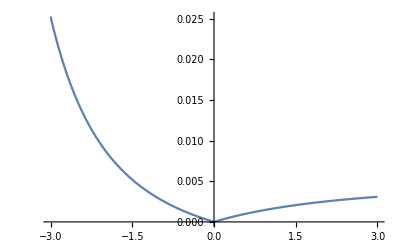

```mathematica
ListLinePlot[Transpose[{epslist,KS}],PlotRange->{Automatic,Full}]
```

```mathematica
Export[NotebookDirectory[]<>"altermu_mu[3]_2.csv",{epslist,mu3Range,matrix, KS}]
```

/home/ez/sense/benchmarks/stan_bench/altermu/altermu_mu[3]_2.csv

```mathematica
SystemOpen["/home/ez/sense/benchmarks/stan_bench/altermu/altermu_mu[3]_2.csv"]
```